```mathematica
createCircle[height_, width_, radius_]:={(height-2*radius)*Random[]+radius, (width-2*radius)*Random[]+radius, radius}
```

```mathematica
addCircle[circleList_, height_, width_, radius_]:=
Module[{newCircle, d, overlap=0},
newCircle=createCircle[height, width, radius];
For[i=1, i≤Length[circleList],
d=Sqrt[(circleList[[i]][[1]]-newCircle[[1]])^2+(circleList[[i]][[2]]-newCircle[[2]])^2];
overlap =If[d<circleList[[i]][[3]] + newCircle[[3]],overlap + 1, overlap];
i++];
If[overlap==0, newCircle, {}]]
```

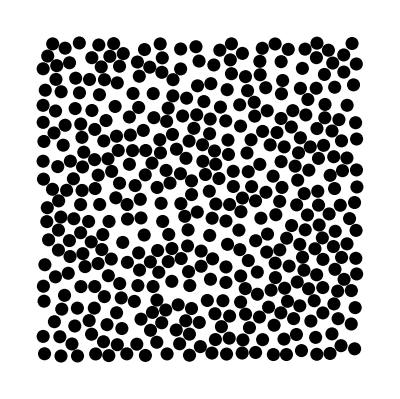
{0.516478,-Graphics-}

```mathematica
L=50;
circleList={createCircle[ L, L, 1]}; 
newCircle=addCircle[circleList, L, L, small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<130000,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L*L))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}
```

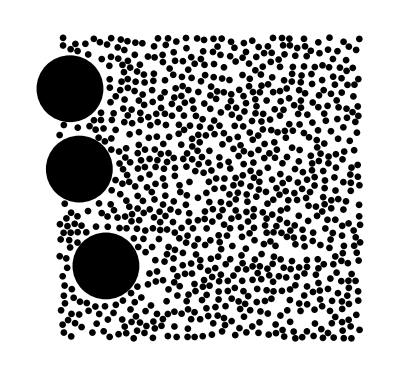
{0.369451,-Graphics-}

```mathematica
big=1;
small=0.1;
h=9;
circleList={createCircle[ L, L, big]}; 
newCircle=addCircle[circleList, L, L, small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<10000,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, big, small]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}
```

```mathematica
runSimulation[iterations_, boxSize_, B_, S_, pB_]:=Module[{},
big=B;
small=S;
circleList={createCircle[ boxSize, boxSize, big]}; 
newCircle=addCircle[circleList, boxSize, boxSize, small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<iterations,
circleList= newCircleList;
newCircle=addCircle[circleList, boxSize, boxSize,If[ Random[]≤ pB, big, small]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((boxSize)*(boxSize))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}]
```

```mathematica
runSimulationSequence[iterations_, boxSize_, B_, S_]:=Module[{big, small, circleList, newCircle, newCircleList},
big=B;
small=S;
circleList={createCircle[ boxSize, boxSize, big]}; 
newCircle=addCircle[circleList, boxSize, boxSize, big];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<iterations,
circleList= newCircleList;
newCircle=addCircle[circleList, boxSize, boxSize,big];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
For[z=1, z<iterations,
circleList= newCircleList;
newCircle=addCircle[circleList, boxSize, boxSize,small];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
{rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((boxSize)*(boxSize))],Graphics[Disk[{#[[1]], #[[2]]}, #[[3]]]&/@newCircleList]}]
```

```mathematica
ans={#,runSimulationSequence[25000, 35, 1, #]}&/@{0.75, 0.5, 0.25, 0.1}
```

Append::normal: Nonatomic expression expected at position 1 in Append[newCircleList$26339765, {19.1458, 25.1395, 1}].

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

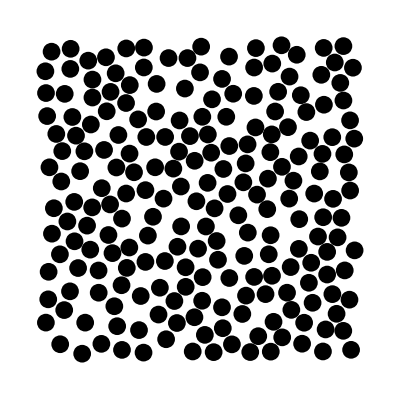
{0.516327,-Graphics-}

```mathematica
runSimulation[10000, 35, 1, 1, 0.9]
```

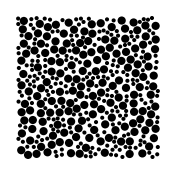
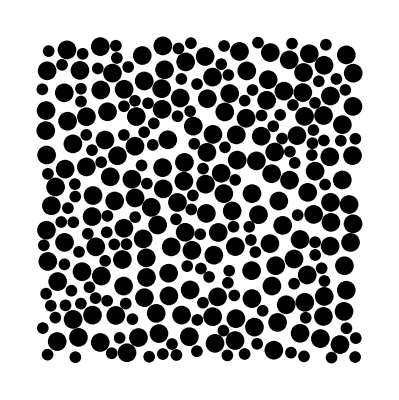
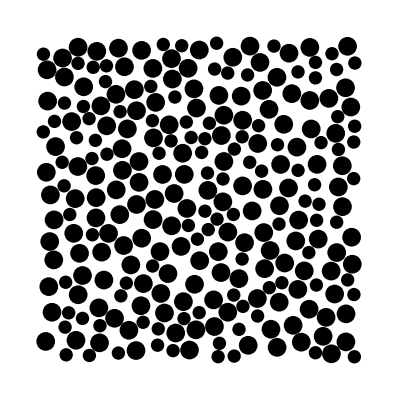
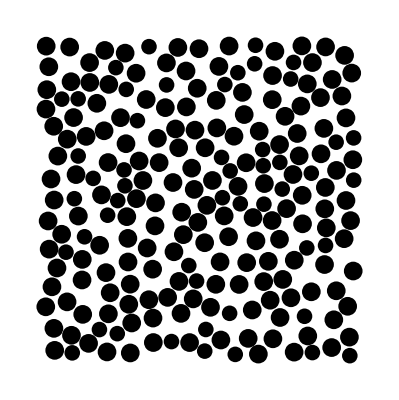
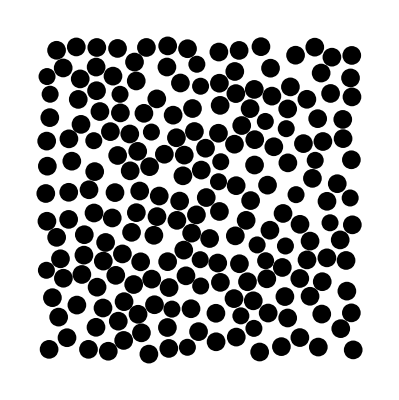
{{1/2,{0.533295,-Graphics-}},{0.625,{0.514849,-Graphics-}},{0.714286,{0.506729,-Graphics-}},{0.833333,{0.491413,-Graphics-}},{0.909091,{0.486416,-Graphics-}}}

```mathematica
{#, runSimulation[60000, 35, 1, #, 0.9]}&/@{1/2,1/ 1.6,1/1.4, 1/1.2, 1/1.1}
```

```mathematica
results =%;
```

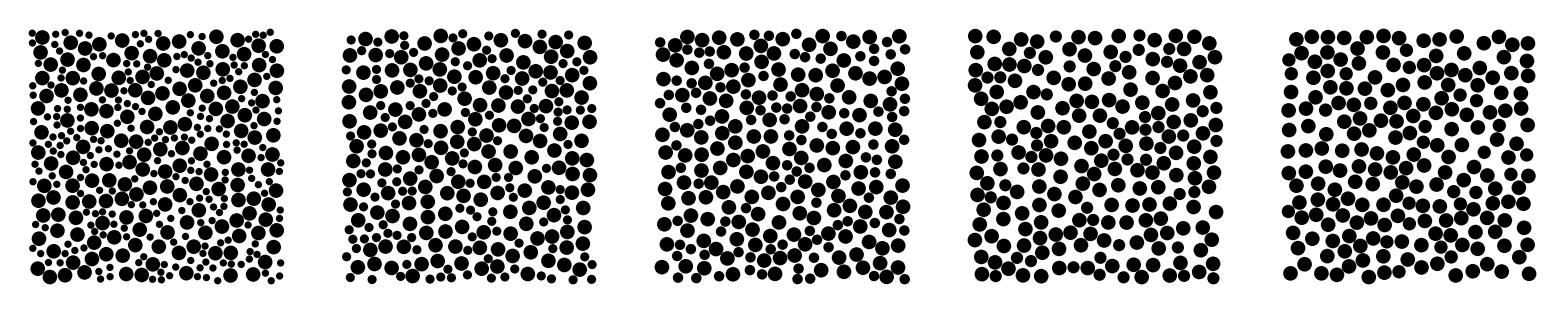

```mathematica
TableForm[{#[[2]][[2]]&/@results}]
```

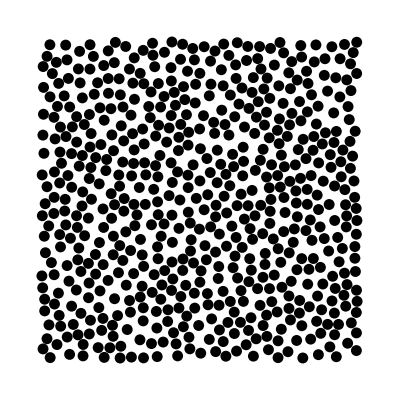
{0.497285,-Graphics-}

```mathematica
runSimulation[120000, 60, 1, 1, 0.9]
```

```mathematica
runSimulation[120000, 60, 1, 0.1, 0.9]
```

$Aborted

This is the main program

```mathematica
L=24;
a=1;
b=0.2;
data={};
For[h=1, h<10, h++,
Print[h];
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<15000,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
data=Append[data, {1-h/10, rho, Length[Select[newCircleList, #[[3]]==a&]], Length[Select[newCircleList, #[[3]]==b&]]}];];
data
```

```mathematica
data={};
For[h=1, h<3, h++,
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList]
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
data=Append[data, {h/10, rho, Length[Select[newCircleList, #[[3]]==a&]], Length[Select[newCircleList, #[[3]]==b&]]}];]
```

{{4.06752,23.1461,1},{7.43894,19.6572,1}}

```mathematica
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
Print[rho];
L=24;
a=1;
b=0.5;
circleList={createCircle[ L, L, a]}; 
newCircle=addCircle[circleList, L, L, 1];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
For[z=1, z<100,
circleList= newCircleList;
newCircle=addCircle[circleList, L, L,If[ Random[]>h/10, a, b]];
newCircleList=If[Length[newCircle]==3, Append[circleList, newCircle], circleList];
z++];
rho=N[Total[Pi*#[[3]]^2&/@newCircleList]/((L+1)*(L+1))];
Print[rho];
```

{{12.096,1.99401,1},{8.45818,10.885,1}}

$Aborted

{}

{{19.7928,20.0749,1},{20.7764,9.7605,1}}

```mathematica
Correlation[{0,0, 1, 1, 1, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0,0}]
```

7/15

```mathematica
?Sound
```

RowBox[{"Sound", "[", StyleBox["primitives", "TI"], "]"}] represents a sound. 
RowBox[{"Sound", "[", RowBox[{StyleBox["primitives", "TI"], ",", StyleBox["t", "TI"]}], "]"}] specifies that the sound should have duration StyleBox["t", "TI"].
RowBox[{"Sound", "[", RowBox[{StyleBox["primitives", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] specifies that the sound should extend from time SubscriptBox[StyleBox["t", "TI"], StyleBox["min", "TI"]] to time SubscriptBox[StyleBox["t", "TI"], StyleBox["max", "TI"]].